```mathematica
(* Change TensorProduct to act like Kronecker product *)
Unprotect[TensorProduct];
TensorProduct=KroneckerProduct;
Protect[TensorProduct];

On[Assert];

(* column vectorize, following Magnus, 1999 *)
vectorize[W_]:=Transpose@{Flatten@Transpose[W]};
unvectorize[Wf_, rows_]:=Transpose[Flatten/@Partition[Wf,rows]];
toscalar[v_]:=Block[{t},
t=Flatten@v;
Assert[Length[t]==1];
First@t
];

vec=vectorize;
unvec=unvectorize;

v2c[c_]:=Transpose[{c}] (* turns vector to column matrix *)
c2v[c_]:=Flatten[c] (* turns column matrix into vector *)

(* Partitions matrix into blocks {{axa,axb},{bxa,bxb}} *)
partitionMatrix[mat_,{a_,b_}]:=Module[{},
Assert[a+b==Length@mat];
Assert;[a+b==Length@matᵀ];
Internal`PartitionRagged[mat,{{a,b},{a,b}}]
];

(* Commutation matrix m,n *)
(* TODO: hide intermediate variables *)
Kmat[m_,n_]:=Module[{x},
X=Array[x,{m,n}];
before=Flatten@vectorize@X;
after=Flatten@vectorize@Transpose[X];
positions=MapIndexed[{First@#2,First@Flatten@Position[before,#]}&,after];
matrix=SparseArray[#->1&/@positions]
];

take1[x_]:=First@Flatten@x;

robustMin[x_]:=Min[Select[Flatten@x,#>1*^-10&]];

(* Symmetric square root *)
symsqrt[m_]:=Module[{U,S,W},
{U,S,W}=SingularValueDecomposition[m];
U.Sqrt[S].Transpose[W]
];


(* divide object by sum of its elements *)
normalize[x_]:=x/Total[x, 10];

(* Random uniform vector normalized to 1 *)
randomD[f_]:=Module[{temp},
temp=RandomReal[{0,1},{f}];
temp/Total[temp]
];

(* centers data where batch dimension is 1 *)
centerData[X_]:=Module[{Xc},
Xc=Mean@Transpose@X;
Transpose[#-Xc&/@Transpose[X]]
];

(* takes sizes [s1,s2,..] partitions vec into those sizes *)
listPartition[list_,sizes_]:=(
Assert[Length@list==Total@sizes, "can't partition"];
offsets={0}~Join~FoldList[Plus,sizes];
offsetPairs=Partition[offsets,2,1];
list[[#[[1]]+1;;#[[2]]]]&/@offsetPairs
);
Assert[listPartition[{1,2,3,4,5},{3,2}]=={{1,2,3},{4,5}}];

(* approximate equality testing *)
DotEqual[a_,b_]:=Norm[Flatten[{a}]-Flatten[{b}]]<1*^-10;
```

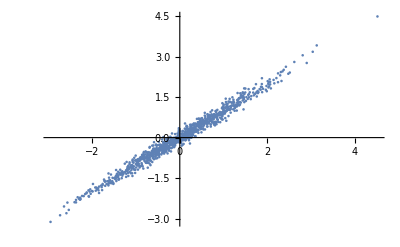

```mathematica
(* Things more specific to natural gradient stuff *)

(* partitions matrix into blocks *)
partitionMatrix2[mat_,sizes_]:=Module[{},
Internal`PartitionRagged[mat,{sizes,sizes}]
];

(* extracts i,j'th block, taking sizes from fsizes *)
matrixBlock[i_,j_,mat_]:=(
msizes=Times@@@(Partition[fs,2,1]//Rest);
partitionMatrix2[mat,msizes][[i,j]]
);

(* extracts i'th block from vector *)
vectorBlock[i_,vec_]:=(
msizes=Times@@@(Partition[fs,2,1]//Rest);
listPartition[vec,msizes][[i]]
);

magnitudeMat[i_,j_,mat_]:=Max[Abs[matrixBlock[i,j,mat]]];
magnitudeVec[i_,vec_]:=Max[Abs[vectorBlock[i,vec]]];


generateXY[e_,yvar_,extraDims_,dsize_]:=Module[{wt,mean,cov,normal,pdf,X,Xc,Y,Xa,wta,w0a,XY,n,trueCov},
SeedRandom[0];
n=2;
wt={{1,1}}; (* true relation *)
mean=0&/@Range@n;
cov={{1, 1-e},{1-e,1}};
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
X=centerData[X];
Y=Dot[wt, X]+RandomVariate[NormalDistribution[0,√yvar]];
(* Add copies of first feature as redundant features *)
Xa= X~Join~Table[X[[1,All]],{i,extraDims}];
wta=Join[wt,{Table[0,{i,extraDims}]}, 2];
w0a=Join[{{1,2}},{Table[0,{i,extraDims}]}, 2];
{Xa,Y,w0a}
];
{X,Y,w0}=generateXY[0.01,1.,0,1000];
ListPlot[Transpose@X]
```

## making single example stats

```mathematica
(* loss with respect to single X *)
lossf1[Wf_,i_]:=
```

```mathematica
(* get single X *)
makeX1[i_]:=v2c[Table[W[0][j,i],{j,fs[[2]]}]];
Join@@(Table[makeX1[i],{i,10}]~Join~{2})==makeW[0]
```

True

```mathematica
makeY1[i_]:=Y[[All,i]];errEq1[i_]:=makeY1[i]-Fold[Dot,Reverse@vars].makeX1[i];
lossEq1[i_]:=(take1[1/(2 dsize)errEq1[i].errEq1[i]ᵀ]);
lossf1[Wf_,i_]:=(lossEq1[i]/.subW[Wf]/.subY/.subX);
gradEq1[i_]:=D[lossf1[Wf,i],{Wf,1}];
gradf1[Wf_,i_]:=gradEq1[i]/.subW[Wf];
```

```mathematica
gradf1[W0f,5]
```

{-0.0308607,-0.0349961}

```mathematica
fisher[Wf_]:=Module[{},
(* dsize x fsize *)
gradList=Table[gradf1[Wf,i],{i,First[fs]}];
gradListᵀ.gradList/dsize
]
```